```mathematica
Grid[Partition[Tooltip[Show[ColorConvert[ColorData[#,"Image"],"RGB"],ImageSize->200],#]&/@ColorData["Gradients"],4,4,1,{}],Spacings->.5];
```

```mathematica
ic[x_]:={1/2 1/(2Zeta[3])(x/2)^2/(Exp[x/2]-1),1/8 Boole[1<x<9],1/2 x^2/Exp[x]}[[1]]
```

```mathematica
color="CMYKColors";
```

```mathematica
ColorConvert[ColorData[color,"Image"],"Grayscale"]
```

-Graphics-

```mathematica
tryCD[s_]:=If[DirectoryQ[s],SetDirectory[s],];
```

```mathematica
tryCD["/home/kasper/Documents/KULeuven/PhD/Photon diffusion"]
```

/home/kasper/Dropbox/Documents/KULeuven/PhD/Photon diffusion

```mathematica
tryCD["/localhome/u0131889/Dropbox/Documents/KULeuven/PhD/Photon diffusion"]
```

```mathematica
Monitor[dataraw={};Do[
AppendTo[dataraw, Import[i]]
,{i,FileNames["data/hist*dat"]}],i];
Monitor[nraw={};Do[
AppendTo[nraw, Import[i]]
,{i,FileNames["data/occu*dat"]}],i];Length[dataraw]
```

11

```mathematica
filename=Import["data/params.txt"]
```

N-1e6.95_t-10_Z-0.9000_reset_rate-0.0010_divisor-60.00

```mathematica
data=dataraw[[{-1}]];
```

```mathematica
data2=Table[{data[[1,i,1]],Mean[data[[;;,i,2]]]},{i,20*20}];
```

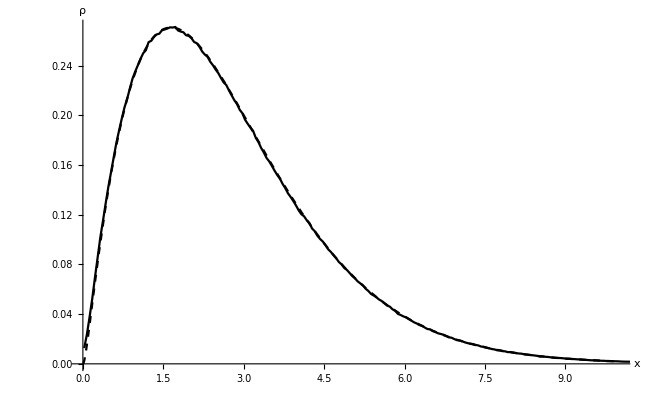

```mathematica
μ=0.0811294;PolyLog[3,E^-μ]/Zeta[3];histplot=Show[
ListPlot[data,PlotRange->{{0,10},All},Joined->True,Ticks->{Automatic,None},AxesLabel->{"x","ρ"},PlotStyle->Black
],
Plot[{1/(2Zeta[3]0.9)x^2/(Exp[x+μ]-1),1/(2Zeta[3]Z[b,k,c])x^2/(Exp[h[x]]-1)},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dashed,Dotted},PlotRange->All,Exclusions->None]
]
```

```mathematica
Export["spd_"<>filename<>".pdf",histplot];
```

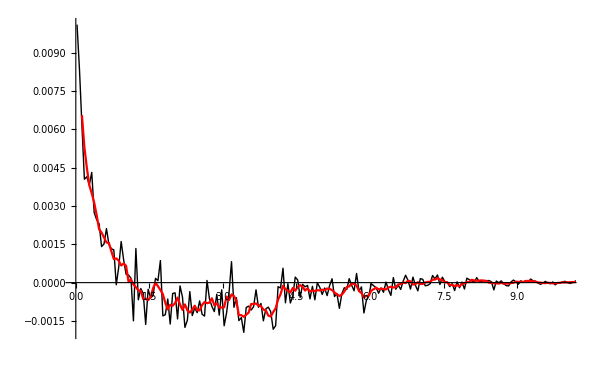

```mathematica
excess={#[[1]],#[[2]]-1/(2Zeta[3]0.9)(#[[1]])^2/(Exp[#[[1]]+μ]-1)}&/@data2[[;;]];excessplot=ListPlot[{excess,MovingAverage[excess,5]},Joined->True,PlotStyle->{{Thin,Black},Red},PlotRange->{{0,10},All}]
```

```mathematica
Export["excess_"<>filename<>".pdf", excessplot];
```

```mathematica
ndata=nraw[[-1;;]];
```

```mathematica
n2=Table[{ndata[[1,i,1]],Mean[ndata[[;;,i,2]]]},{i,20*20}];
```

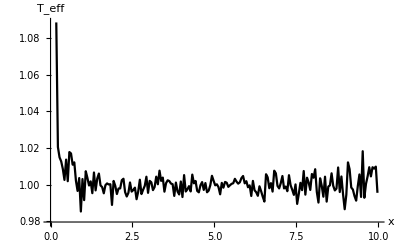

```mathematica
tplot=Show[
ListPlot[Last@TakeList[{#[[1]],(#[[1]]+μ)/Log[1+1/(#[[2]])]}&/@(n2[[1;;10*20]]),{3,All}],PlotRange->{All,All},Joined->{True,False},PlotTheme->"Monochrome",AxesLabel->{"x","T_eff"},PlotMarkers->None]]
```

```mathematica
Export["temp_" <> filename <> ".pdf", tplot]
```

temp_N-1e5.95_t-10_Z-0.9000_reset_rate-0.0001_interval-0.10.pdf

```mathematica
ns=Import["data/n.dat"];
```

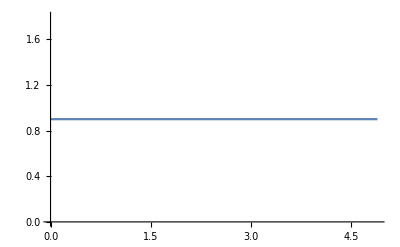

```mathematica
nplot=Show[
ListPlot[ns[[;;;;100]],PlotLegends->Automatic,Joined->True,PlotRange->All],
Plot[{Z[b,k,c]},{x,0,1000},PlotTheme->"Monochrome"]
]
```

```mathematica
Export["n "<>filename<>".pdf",nplot];
```

```mathematica
c=1/100;b=00/100;k=4/10;
```

```mathematica
x0=1/10;
```

```mathematica
h[x_]:=NIntegrate[Piecewise[{{1,s<=x0},{1+b s^k,s>x0}}]/(1+Piecewise[{{0,s<=x0},{c/s^3,s>x0}}]),{s,0,x}]
```

```mathematica
Clear[Z];Z[b_,k_,c_]:=Z[b,k,c]=Module[{h2},
h2[x_]:=NIntegrate[Piecewise[{{1,s<=x0},{1+b s^k,s>x0}}]/(1+Piecewise[{{0,s<=x0},{c/s^3,s>x0}}]),{s,0,x}];
NIntegrate[1/(2Zeta[3])xx^2/(Exp[h2[xx]]-1),{xx,0,∞}]]
```

```mathematica
pplot=histplot=Show[
ListPlot[data2,PlotRange->{{0,10},All},Joined->True,PlotStyle->Table[ColorData[color,i/(Length[data]-1)],{i,0,Length[data]-1}],(*PlotLegends->BarLegend[{"CMYKColors",{0,2}}],*)Ticks->{Automatic,None},AxesLabel->{"x","ρ"}
],
Plot[{1/(2Zeta[3])x^2/(Exp[x]-1)(*,1/(2Zeta[3]Z[b,k,c])x^2/(Exp[h[x]]-1)*)},{x,0,10},PlotTheme->"Monochrome",PlotStyle->{Dotted},PlotRange->All,Exclusions->None]
]
```

```mathematica
Export["compare " <>filename<>".pdf",pplot]
```

compare N-1e5.70 dx-0.05 t-100 dt-0.0001 ic-planck c-0.1000 brems.pdf

```mathematica
NDSolve[{
D[u[t,x],t]==D[u[t,x],x,x]-u[t,x]+10u[t,10x],
u[0,x]==Exp[-x^2/2],u[t,-20]==u[t,+20]==0},u,{x,-20,+20},{t,0,10}]
```

NDSolve::conarg: The arguments should be ordered consistently.

NDSolve::delpde: Delay partial differential equations are not currently supported by NDSolve.

NDSolve[{u^(1,0)[t,x]==-u[t,x]+10 u[t,10 x]+u^(0,2)[t,x],u[0,x]==ⅇ^(-x^2/2),u[t,-20]==u[t,20]==0},u,{x,-20,20},{t,0,10}]

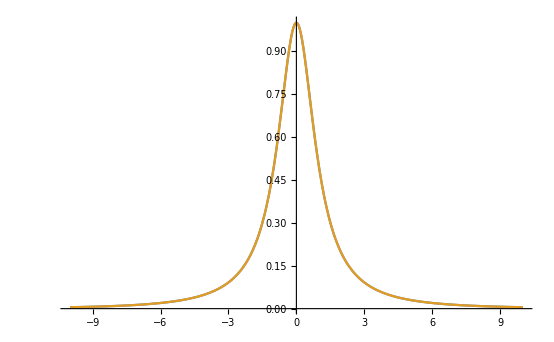

```mathematica
Plot[{1/QPochhammer[-k^2,1/100],1/QPochhammer[-(k/10)^2,1/100](1+k^2)^-1},{k,-10,+10},PlotRange->All]
```

```mathematica
Product[1/(1+(k/10^m)^2)1/10^m,{m,0,∞}]
```

0

```mathematica
f[x_]:=NIntegrate[1/(2π QPochhammer[-k^2,1/100])Exp[-I k x],{k,-∞,+∞}]
```

```mathematica
f[1]
```

0.185814+0. ⅈ

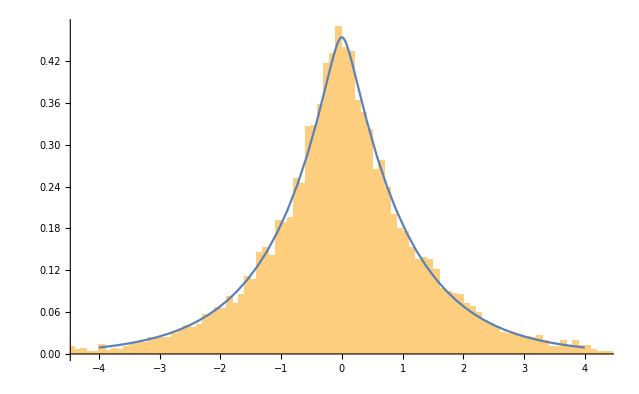

```mathematica
Show[
Histogram[a,{0.1},"PDF"],
Plot[f[x],{x,-4,+4}]]
```

```mathematica
NIntegrate[f[x],{x,-4,+4}]
```

0.981498

```mathematica
f''[1]
```

0.185585

```mathematica
-f[1]+10f[10]
```

-0.185923+0. ⅈ

```mathematica
a=Flatten[Import["xs.dat"]]
```

{2.45932,0.294932,-0.291753,-0.509634,-0.807334,0.227837,0.423358,-3.43479,-2.26188,0.10203,-0.984877,-0.066589,0.644542,-0.61649,-1.81009,9970,-0.691214,6.54136,0.160712,-0.405029,-0.076223,0.262968,0.157144,-3.34778,1.95963,0.069928,-0.263714,-0.726408,1.85632,1.55055,2.02473}
 |  |  |  |

```mathematica
a
```

{2.45932,0.294932,-0.291753,-0.509634,-0.807334,0.227837,0.423358,-3.43479,-2.26188,0.10203,-0.984877,-0.066589,0.644542,-0.61649,-1.81009,9970,-0.691214,6.54136,0.160712,-0.405029,-0.076223,0.262968,0.157144,-3.34778,1.95963,0.069928,-0.263714,-0.726408,1.85632,1.55055,2.02473}
 |  |  |  |

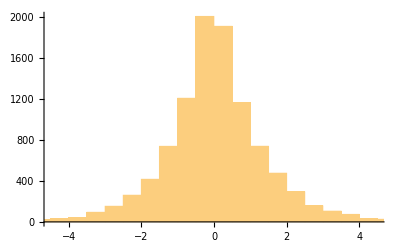

```mathematica
Histogram[a]
```

```mathematica
GeoGraphics[NightHemisphere[],GeoRange->All]
```

-Graphics-